```mathematica
ClearAll["Global`*"]
(*別のnbファイルの内容を取り込み，後で利用する*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]];
names={"dataMP1d5piston1.csv","dataMP1d5piston2.csv"};(*実験固有周期0.566,　Molin2018 = 0.71986*)
(*names={"dataMP3d0piston1.csv","dataMP3d0piston2.csv"};(*0.8?, 0.6477*)
names={"dataMP5d0piston1.csv","dataMP5d0piston2.csv"};(*0.9?, 0.5937*)

names={"dataMP1d5pitch1.csv","dataMP1d5pitch2.csv"};(*0.63, Molinスロッシング = 0.52617*)
names={"dataMP3d0pitch1.csv","dataMP3d0pitch2.csv"};(*0.672, 0.3942*)
names={"dataMP5d0pitch1.csv","dataMP5d0pitch2.csv"};(*0.685, 0.3093*)
*)

files=Table["実験結果20250210/"<>names[[i]],{i,1,Length@names}]

DATA=Table[Import[FileNameJoin[{NotebookDirectory[],files[[i]]}],"CSV"],{i,1,Length[files],1}];
colorFunc=Blend[{Cyan,Blue,Red},#/Length[DATA]]&;
colorPitch=Blend[{Cyan,Blue,Red},#/Length[DATA]]&;
colorHeave=Blend[{Yellow,Red,Black},#/Length[DATA]]&;
```

{実験結果20250210/dataMP1d5piston1.csv,実験結果20250210/dataMP1d5piston2.csv}

```mathematica
(*Molin (2018)*)
B1=15;(*ムーンプールの幅*)
B2=45;(*浮体の幅*)
L1=B1;(*ムーンプールの長さ*)
L2=B2;(*浮体の長さ*)
d=12;(*喫水*)
c=80.;(*水深*)
a=(L2-L1)/2.;
b=(B2-B1)/2.;
g=9.81;
Print["Tsloshing=",TSloshingMolin2018[B1,B2,L1,L2,d,c,300]]
Print["Tpiston=",TPistonMolin2018[B1,B2,L1,L2,d,c,300]]
```

Tsloshing=4.3763

Tpiston=8.46188

```mathematica
(*30 Tp=9.12*)
(*15 Tp=8.4*)
(*9 Tp=7.972*)
```

```mathematica
37.5/5
```

7.5

```mathematica
(*関数定義*)
calculate[data_]:=Module[{min,max,m,initxaxis,inityaxis,ans,initzaxis,CameraM,anlgetable,timetable,a00,a01,a02,a10,a11,a12,a20,a21,a22,displacement,initCOM,COM,Wfloat,initrage},
min=65;
max=120;
initrage={10,min};
max=If[max>Length[data],Length[data],max];
ydir[i_]:=Normalize[data[[i]][[8;;10]]-data[[i]][[2;;4]]];
zdir[i_]:=Normalize[Cross[data[[i]][[5;;7]]-data[[i]][[2;;4]],data[[i]][[8;;10]]-data[[i]][[2;;4]]]];
xdir[i_]:=Normalize[Cross[zdir[i],ydir[i]]];
initxaxis=Mean[Table[xdir[i],{i,initrage[[1]],initrage[[2]]}]];
inityaxis=Mean[Table[ydir[i],{i,initrage[[1]],initrage[[2]]}]];
initzaxis=Mean[Table[zdir[i],{i,initrage[[1]],initrage[[2]]}]];
(*カメラの座標系から水槽x,y,z座標へ変換するための，回転行列を計算する*)
m={{a00,a01,a02},{a10,a11,a12},{a20,a21,a22}};
ans=Quiet@FindMinimum[Norm[m.initxaxis-{1,0,0}]+Norm[m.inityaxis-{0,1,0}]+Norm[m.initzaxis-{0,0,1}],{a00,a01,a02,a10,a11,a12,a20,a21,a22}];
CameraM=m/.ans[[2]];
(*table=Table[{data[[i,1]],VectorAngle[M.zdir[i],{0,0,1}]},{i,1,100}];*)
(*displacement=Table[M.(data[[i]][[2;;4]]-data[[1]][[2;;4]]+data[[i]][[5;;7]]-data[[1]][[5;;7]]+data[[i]][[8;;10]]-data[[1]][[8;;10]]),{i,min,max}];*)
Wfloat=37.5*10;
COM[i_]:=Wfloat/2*xdir[i]+(data[[i]][[2;;4]]+data[[i]][[5;;7]])/2-96/2*zdir[i];
initCOM=Mean[Table[COM[i],{i,initrage[[1]],initrage[[2]]}]];

displacement=Table[CameraM.(COM[i]-initCOM),{i,min,max}];
(*anlgetable=Table[VectorAngle[CameraM.zdir[i],{0,0,1}],{i,min,max}];*)
anlgetable=Table[VectorAngle[zdir[i],initzaxis],{i,min,max}];
timetable=data[[min;;max,1]];
{displacement,anlgetable,timetable,CameraM,{initxaxis,inityaxis,initzaxis},{min,max}}
]
```

```mathematica
inv[x_]:=If[Abs[x]>10^-10,1/x,1/10^-10];
```

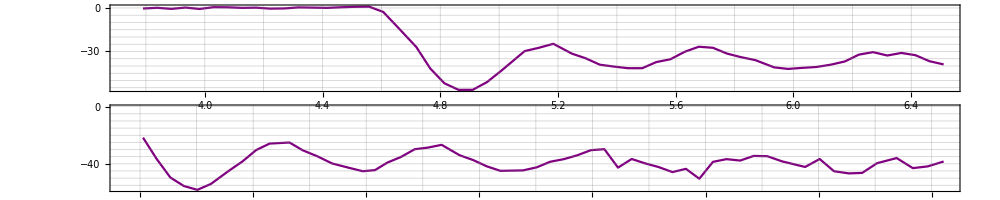

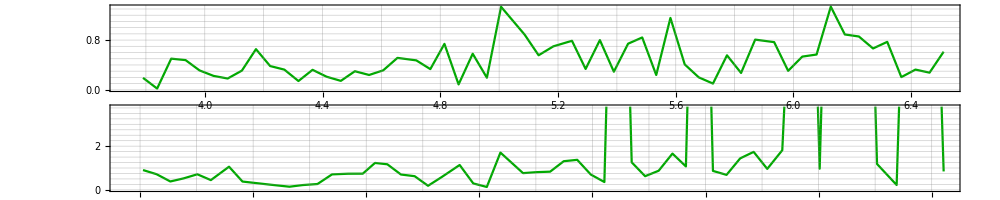

```mathematica
GraphicsColumn[Table[
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
ListPlot[Transpose[{timetable,displacement[[;;,3]]}],ImageSize->800,AspectRatio->1/10
(*,PlotRange->{{8,18},{-10,10}}*)
,GridLines->All,PlotLegends->Automatic,Evaluate[plot2Doption]
,PlotStyle->Purple(*FrameLabel->{"Time [s]","Heave [mm]"},*)
(*,Epilog->names[[i]]*)
],{i,1,Length[DATA]}]
,Spacings->0
,ImageSize->1000
]

GraphicsColumn[Table[
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
ListPlot[Transpose[{timetable,anlgetable/π*180}]
,ImageSize->800
,AspectRatio->1/10
(*,PlotRange->{{8,18},{-10,10}}*)
,Evaluate[plot2Doption]
,GridLines->All(*,FrameLabel->{"Time [s]","Pitch Angle [rad]"}*)
,ImageSize->Large
,PlotStyle->Darker[Green]
],{i,1,Length[DATA]}]
,Spacings->0
,ImageSize->1000
]
```

## ピッチ

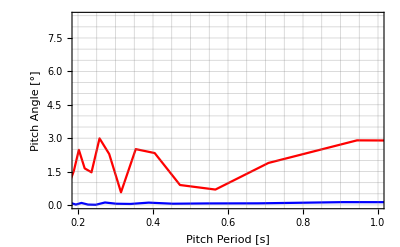

```mathematica
(*フーリエ解析*)
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2/π*180}&@@@interpolateAndFourier[timetable,anlgetable]]]
,{i,1,Length@DATA,1}]
(*,PlotLegends->names*)
,GridLines->All
,PlotRange->{{0.2,1},{0,All}}
,Evaluate[plot2Doption]
,FrameLabel->{"Pitch Period [s]","Pitch Angle [°]"}
,PlotStyle->Table[colorFunc[i],{i,1,Length[DATA]}]
]
```

```mathematica
option3D={Filling->Axis
,ViewPoint->{-Pi,-Pi,Pi/2}
,PlotStyle->Black
(*,PlotLegends->Placed[names, Top]*)
,LabelStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->18]
,PlotRange->Automatic
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->18]
,ImageSize->600
,AxesStyle->Black
,Axes->True};
```

```mathematica
ListLinePlot3D[
Table[
Module[{tmp},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
tmp=interpolateAndFourier[timetable,anlgetable];
Table[{0.01*periods[[i]],inv@tmp[[j]][[1]],tmp[[j]][[2]]/π*180},{j,1,Length@tmp}]
]
,{i,1,Length@DATA,1}]
,ImageSize->Large
,ViewPoint->{-Pi,Pi,2}
,PlotRange->{All,{0.2,1},{0,1.6}}
,ScalingFunctions->{Identity,"Reverse",Identity}  (*y軸だけを反転*)
,AxesLabel->{"Incident Wave Period [s]","Pitch Period [s]",Rotate["Pitch Angle [°]",π/2]}
,PlotStyle->Table[colorFunc[i],{i,1,Length[DATA]}]
,Evaluate[option3D]
]
```

Part::partd: 部分指定periods⟦1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: {}の部分3は存在しません．

-Graphics3D-

## ヒーブ

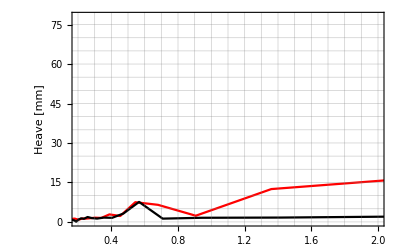

```mathematica
(*フーリエ解析*)
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2}&@@@interpolateAndFourier[timetable,displacement[[;;,3]]]]]
,{i,1,Length@DATA,1}]
,GridLines->All
,PlotRange->{{0.2,2},All}
,Evaluate[plot2Doption]
,PlotStyle->Table[colorHeave[i],{i,1,Length[DATA]}]
,FrameLabel->{""(*"Heave Period [s]"*),"Heave [mm]"}
]
```

```mathematica
ListLinePlot3D[
Table[
Module[{tmp},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
tmp=interpolateAndFourier[timetable,displacement[[;;,3]]];
Table[{0.01*periods[[i]],inv@tmp[[j]][[1]],tmp[[j]][[2]]},{j,1,Length@tmp}]
]
,{i,1,Length@DATA,1}]
,ImageSize->Large
,ViewPoint->{-Pi,Pi,2}
,PlotRange->{All,{0.2,1},{0,5}}  (*y軸を反転させる*)
 ,ScalingFunctions->{Identity,"Reverse"}  (*y軸だけを反転*)
,PlotStyle->Table[colorHeave[i],{i,1,Length[DATA]}]
,AxesLabel->{""(*"Incident Wave Period [s]"*),""(*"Heave Period [s]"*),Rotate["Heave [mm]",π/2]}
,Evaluate[option3D]
]
```

Part::partd: 部分指定periods⟦1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: {}の部分3は存在しません．

-Graphics3D-

```mathematica
data=DATA[[1]];
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[data];
center[i_]:=(data[[i]][[2;;4]]+data[[i]][[5;;7]]+data[[i]][[8;;10]])/3;
center0=center[1];
trfm[xyz_]:=M.(xyz-center0);
o={0,0,0};

Show[
{ListPointPlot3D[
{Table[trfm@data[[i]][[2;;4]],{i,min,max}],
Table[trfm@data[[i]][[5;;7]],{i,min,max}],
Table[trfm@data[[i]][[8;;10]],{i,min,max}]}
,BoxRatios->{1, 1, 1}
,AxesLabel->{"x","y","z"}
,PlotRange->{{-300,300},{-300,300},{-300,300}}
],
Graphics3D[Table[Line[{trfm@data[[i]][[2;;4]],trfm@data[[i]][[5;;7]],trfm@data[[i]][[8;;10]],trfm@data[[i]][[2;;4]]}],{i,min,max}]],
Graphics3D[{Red,Arrow[{o,o+200*xaxis}]}],
Graphics3D[{Blue,Arrow[{o,o+200*yaxis}]}],
Graphics3D[{Green,Arrow[{o,o+200*zaxis}]}]
}
,BoxRatios->{1, 1, 1}
,AxesLabel->{"x","y","z"}
,FrameTicks->True
,PlotRange->{{-300,300},{-300,300},{-300,300}}
];

Manipulate[
Show[
ListPointPlot3D[
{{trfm@data[[i]][[2;;4]]},
{trfm@data[[i]][[5;;7]]},
{trfm@data[[i]][[8;;10]]}}
,PlotLabel->data[[i]][[1]]
,PlotStyle->{Red,Blue,Green}
,PlotLabel->data[[i]][[1]]
,PlotRange->{{-300,300},{-300,300},{-300,300}}
,BoxRatios->{ 1, 1,1}
,AxesLabel->{"x","y","z"}
],
Graphics3D[{Thick,Line[{trfm@data[[i]][[2;;4]],trfm@data[[i]][[5;;7]],trfm@data[[i]][[8;;10]],trfm@data[[i]][[2;;4]]}]}],
Graphics3D[{Red,Arrow[{o,o+300*M.xaxis}]}],
Graphics3D[{Blue,Arrow[{o,o+300*M.yaxis}]}],
Graphics3D[{Green,Arrow[{o,o+300*M.zaxis}]}],
Graphics3D[{Purple,Thick,Arrow[{trfm@center[i],trfm@center[i]+300*M.zdir[i]}]}]
]
,{i,min,max,1}]

Show@Table[
Show[
ListPointPlot3D[
{{trfm@data[[i]][[2;;4]]},
{trfm@data[[i]][[5;;7]]},
{trfm@data[[i]][[8;;10]]}}
,PlotLabel->data[[i]][[1]]
,PlotStyle->{Red,Blue,Green}
,PlotLabel->data[[i]][[1]]
,PlotRange->{{-300,300},{-300,300},{-300,300}}
,BoxRatios->{ 1, 1,1}
,AxesLabel->{"x","y","z"}
],
Graphics3D[{Thick,Line[{trfm@data[[i]][[2;;4]],trfm@data[[i]][[5;;7]],trfm@data[[i]][[8;;10]],trfm@data[[i]][[2;;4]]}]}],
Graphics3D[{Red,Arrow[{o,o+300*M.xaxis}]}],
Graphics3D[{Blue,Arrow[{o,o+300*M.yaxis}]}],
Graphics3D[{Green,Arrow[{o,o+300*M.zaxis}]}],
Graphics3D[{Purple,Thick,Arrow[{trfm@center[i],trfm@center[i]+300*M.zdir[i]}]}]
]
,{i,min,max,10}]
```

-Graphics3D-